```mathematica
Clear["Global`*"]
```

# Non-zero temperature Conductance vs Bias NS junction

```mathematica
t=1.0; (*Lattice constant*)
B=1.7; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0000001; (*Imaginary off-set*)
Ln=0;

HR={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HL={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=-0.02; (*Minimal bias value*)
eVmax=0.02; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=401; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	(*Fermi functions*)
	FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
	Fμ=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω+eV],T],FermiFunction[Re[ω+eV],T]}];
	F=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T]}];
	U=DiagonalMatrix[{1,1,0,0}];
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω Id-HL];ϵL=HL;ϵSL=HL;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω Id-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω Id-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω Id-HR];ϵR=HR;ϵSR=HR;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω Id-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω Id-ϵSR];
	
	Do[
		gLLr=Inverse[ω Id-HL-τ^2 V10.gLLr.V01];
	,{i,1,Ln}];
	
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];

		
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	gLLPM=(gLLa-gLLr).Fμ;
	gRRPM=(gRRa-gRRr).F;
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

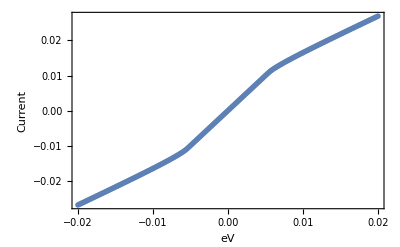

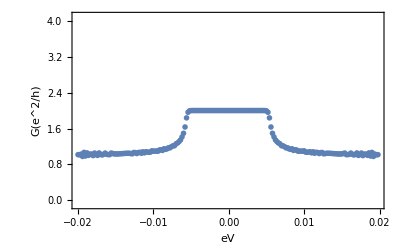

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Meir–Wingreen Formula

```mathematica
Clear["Global`*"]
```

```mathematica
t=1.0; (*Lattice constant*)
B=1.7; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0000001; (*Imaginary off-set*)
Ln=0;

HR={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HL={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=-0.02; (*Minimal bias value*)
eVmax=0.02; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,eV_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[-ω-eV],T],1-FermiFunction[Re[-ω-eV],T]}];
U=DiagonalMatrix[{1,1,-1,-1}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];

ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω Id-HR];ϵL=HR;ϵSL=HR;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω Id-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω Id-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω Id-HR];ϵR=HR;ϵSR=HR;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω Id-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω Id-ϵSR];
	
	Do[
		gLLr=Inverse[ω Id-HL-τ^2 V10.gLLr.V01];
	,{i,1,Ln}];
	
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];
	
	gLesserL=-F[ω,eV,T].(gLLr-gLLa);
	gLesserR=-F[ω,0,T].(gRRr-gRRa);
	
	ΣLesserL=V10.gLesserL.V01;
	ΣLa=V10.gLLa.V01;
	ΣLesserR=V01.gLesserR.V10;
	
	G=Inverse[ω Id-HL-V10.gLLr.V01-V01.gRRr.V10];
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).U]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

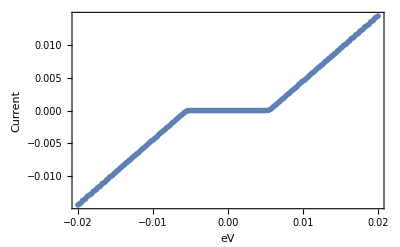

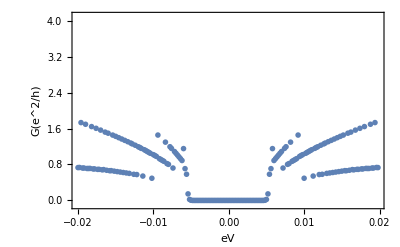

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Meir–Wingreen Formula 8x8 Matrices

```mathematica
Clear["Global`*"]
```

```mathematica
t=1.0; (*Lattice constant*)
B=1.7; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0000001; (*Imaginary off-set*)
Ln=0;

Hr={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
Hl={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
HR=KroneckerProduct[IdentityMatrix[2],Hr];
HL=KroneckerProduct[IdentityMatrix[2],Hl];
V01=KroneckerProduct[IdentityMatrix[2],{{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}}];
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[8];

eVmin=-0.02; (*Minimal bias value*)
eVmax=0.02; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=401; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,eV_,T_]:=KroneckerProduct[IdentityMatrix[2],DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[-ω-eV],T],1-FermiFunction[Re[-ω-eV],T]}]];
U=DiagonalMatrix[{1,1,-1,-1,1,1,-1,-1}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];

ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω Id-HL];ϵL=HL;ϵSL=HL;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω Id-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω Id-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω Id-HR];ϵR=HR;ϵSR=HR;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω Id-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω Id-ϵSR];
	
	Do[
		gLLr=Inverse[ω Id-HL-τ^2 V10.gLLr.V01];
	,{i,1,Ln}];
	
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];
	
	gLesserL=-F[ω,eV,T].(gLLr-gLLa);
	gLesserR=-F[ω,0,T].(gRRr-gRRa);
	
	ΣLesserL=V10.gLesserL.V01;
	ΣLa=V10.gLLa.V01;
	ΣLesserR=V01.gLesserR.V10;
	
	G=Inverse[ω Id-HL-V10.gLLr.V01-V01.gRRr.V10];
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).U]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=(1/2)Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.995291+25660. ⅈ,-1.30453-25800.9 ⅈ,-0.0767818-25800.9 ⅈ,0.000052798-25660. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{«1»},«4»,{«1»},{0.+0. ⅈ,0.+0. ⅈ,«5»,0.995185+25660. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

-Graphics-

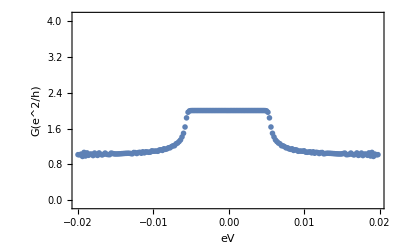

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Non-zero temperature Conductance vs Bias SNS junction

```mathematica
Clear["Global`*"]
```

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.0; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=2.0; (*Chemical potential of the left lead*)
μR=2.0; (*Chemical potential of the right lead*)
T=0.00001; (*Temperature*)
η=0.000001; (*Imaginary off-set*)
Ln=1;

HR={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HL={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=-0.2; (*Minimal bias value*)
eVmax=0.2; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=301; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	(*Fermi functions*)
	FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
	Fμ=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω+eV],T],FermiFunction[Re[ω+eV],T]}];
	F=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T]}];
	U=DiagonalMatrix[{1,1,0,0}];
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω Id-HR];ϵL=HR;ϵSL=HR;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω Id-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω Id-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω Id-HR];ϵR=HR;ϵSR=HR;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω Id-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω Id-ϵSR];
	
	Do[
		gLLr=Inverse[ω Id-HL-τ^2 V10.gLLr.V01];
		gRRr=Inverse[ω Id-HL-τ^2 V01.gRRr.V10];
	,{i,1,Ln}];
	
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];

		
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	gLLPM=(gLLa-gLLr).Fμ;
	gRRPM=(gRRa-gRRr).F;
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

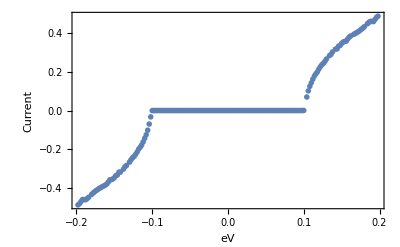

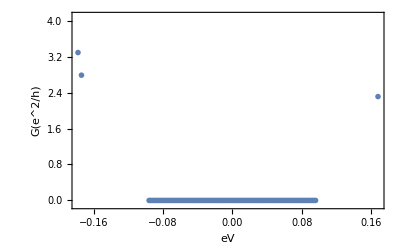

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Current Rashba wire new method

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.0; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=2.0; (*Chemical potential of the left lead*)
μR=2.0; (*Chemical potential of the right lead*)
T=0.001; (*Temperature*)
η=0.00001; (*Imaginary off-set*)
Ln=10;

HR={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HL={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=-0.15; (*Minimal bias value*)
eVmax=0.15; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	(*Fermi functions*)
	FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
	Fμ=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω+eV],T],FermiFunction[Re[ω+eV],T]}];
	F=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T]}];
	U=DiagonalMatrix[{1,1,0,0}];
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω Id-HL];ϵL=HL;ϵSL=HL;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω Id-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω Id-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω Id-HR];ϵR=HR;ϵSR=HR;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω Id-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω Id-ϵSR];
	
	Do[
		gLLr=Inverse[ω Id-HL-τ^2 V10.gLLr.V01];
	,{i,1,Ln}];
	
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];

		
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	gLLPM=(gLLa-gLLr).Fμ;
	gRRPM=(gRRa-gRRr).F;
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Floquet Current (First try)

```mathematica
4 2(24+1)
```

200

```mathematica
Clear["Global`*"]
```

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction*)
α=0.05; (*Spin-orbit coupling*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0; (*Temperature*)
η=0.00001; (*Imaginary off-set*)
Ln=2;
```

```mathematica
HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

Id=IdentityMatrix[4];

FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
Fμ[ω_]:=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω+eV],T],FermiFunction[Re[ω+eV],T]}];
F[ω_]:=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],FermiFunction[Re[ω],T]}];
U=DiagonalMatrix[{1,1,0,0}];

Floquet[Op_,Shift_,Coupling_,nBand_]:=Module[{nFloq,IdOp},
	nFloq=2 nBand+1;
	IdOp=IdentityMatrix[Length[Op]];
	ArrayFlatten[Table[Which[
		n==m,Op+Shift (n-1-nBand) eV IdOp,
		n==m+1,Coupling V10,
		n==m-1,Coupling V01,
		True, ConstantArray[0,Dimensions[Op]]],
	{n,nFloq},{m,nFloq}]]];
	

nBand=12;
IdFloq=IdentityMatrix[4 (2 nBand+1)];

HFloqN=Floquet[HN,1,1,nBand];
HFloqS=Floquet[HS,1,0,nBand];  
V01Floq=Floquet[V01,0,0,nBand]; 
V10Floq=Floquet[V10,0,0,nBand]; 
UFloq=Floquet[U,0,0,nBand];  
FμFloq[ω_]:=Floquet[Fμ[ω],0,0,nBand];
FFloq[ω_]:=Floquet[F[ω],0,0,nBand];

ΣLRr=V01Floq;
ΣRLr=V10Floq;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];


eVmin=-0.0; (*Minimal bias value*)
eVmax=0.15; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
τ=Sqrt[0.05];
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>=0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
SetSharedVariable[Current];
LaunchKernels[]; 
ParallelDo[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	it=1000;
	(* Semiinfinite metal on the left side.*)
	gL=Inverse[ω IdFloq-HFloqN];ϵL=HFloqN;ϵSL=HFloqN;αL=V10Floq;βL=V01Floq;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[ω IdFloq-ϵL];
		If[Max[Abs[αL]]<10^-20,Break[];],{i,1,it}];			
	gLLr=Inverse[ω IdFloq-ϵSL];

	(* Semiinfinite superconductor on the right side *)		
	gR=Inverse[ω IdFloq-HFloqS];ϵR=HFloqS;ϵSR=HFloqS;αR=V01Floq;βR=V10Floq;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[ω IdFloq-ϵR];
		If[Max[Abs[αR]]<10^-20,Break[];
		],{i,1,it}];			
	gRRr=Inverse[ω IdFloq-ϵSR];
	
	Do[
		gLLr=Inverse[ω IdFloq-HFloqN-τ^2 V10Floq.gLLr.V01Floq];
	,{i,1,Ln}];
	(*Calculate the advanced Green's functions*)
	gRRa=ConjugateTranspose[gRRr];
	gLLa=ConjugateTranspose[gLLr];

		
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	gLLPM=(gLLa-gLLr).FμFloq[ω];
	gRRPM=(gRRa-gRRr).FFloq[ω];
	GRRa=Inverse[IdFloq-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[IdFloq-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(IdFloq+GRLr.ΣLRr).gRRPM.(IdFloq+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).UFloq]];

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];

SetDirectory[NotebookDirectory[]];
CPlot=ListLinePlot[CurrentList];
Export["FloquetCurrent_22.07.2025_DifferentHs_n="<>ToString[nBand]<>"_τ="<>ToString[τ]<>"_B="<>ToString[B]<>".mx",CurrentList]
Export["FloquetCurrent_22.07.2025_DifferentHs_n="<>ToString[nBand]<>"_τ="<>ToString[τ]<>"_B="<>ToString[B]<>".png",CPlot]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

General::stop: Further output of LaunchKernels::nodef will be suppressed during this calculation.

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

FloquetCurrent_22.07.2025_DifferentHs_n=12_τ=0.223607_B=0..mx

FloquetCurrent_22.07.2025_DifferentHs_n=12_τ=0.223607_B=0..png

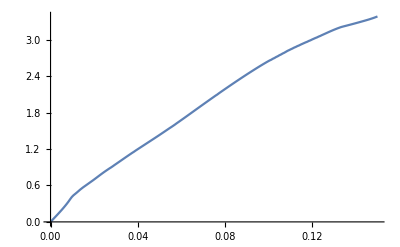

```mathematica
ListLinePlot[CurrentList]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FloquetCurrent_n="<>ToString[nBand]<>".mx",CurrentList]
```

FloquetCurrent_n=24.mx

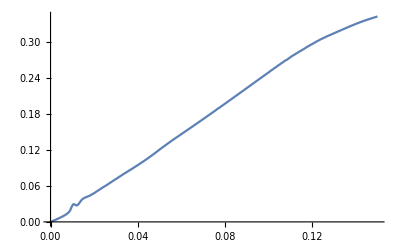

```mathematica
ListLinePlot[CurrentList]
```

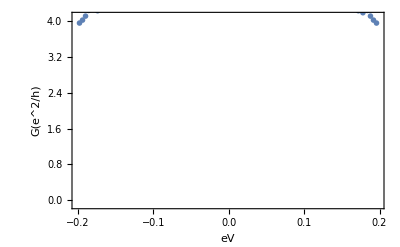

```mathematica
(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]
```

# Floquet Current

```mathematica
Clear["Global`*"]
```

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.0; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=2.0; (*Chemical potential of the left lead*)
μR=2.0; (*Chemical potential of the right lead*)
T=0.001; (*Temperature*)
η=0.00001; (*Imaginary off-set*)

HS={{2t-μS,B,0,0},{B,2t-μS,0,0},{Δ,0,-(2t-μS),B},{0,0,B,-(2t-μS)}};
HN={{2t-μN,B,Δ,0},{B,2t-μN,0,Δ},{Δ,0,-(2t-μN),B},{0,Δ,B,-(2t-μN)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=-0.15; (*Minimal bias value*)
eVmax=0.15; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
gLInf[ω_,HS_,V01_,V10_,η_,it_]:=Module[{gL,ϵL,ϵSL,αL,βL,Id},
	Id=IdentityMatrix[Length[HS]];
	gL=Inverse[(ω + I η)Id-HS]; ϵL=HS;ϵSL=HS;αL=V10;βL=V01;
	Do[ϵSL=ϵSL+αL.gL.βL;ϵL=ϵL+αL.gL.βL+βL.gL.αL;αL=αL.gL.αL;βL=βL.gL.βL;gL=Inverse[(ω + I η) Id-ϵL];
		If[Max[Abs[αL]]<10^-15,Break[];],{i,1,it}];
	Inverse[(ω + I η) Id-ϵSL]
]

gRInf[ω_,HS_,V01_,V10_,η_,it_]:=Module[{gR,ϵR,ϵSR,αR,βR,Id},
	Id=IdentityMatrix[Length[HS]];
	gR=Inverse[(ω + I η)Id-HS]; ϵR=HS;ϵSR=HS;αR=V01;βR=V10;
	Do[ϵSR=ϵSR+αR.gR.βR;ϵR=ϵR+αR.gR.βR+βR.gR.αR;αR=αR.gR.αR;βR=βR.gR.βR;gR=Inverse[(ω + I η)Id-ϵR];
		If[Max[Abs[αR]]<10^-15,Break[];],{i,1,it}];
	Inverse[(ω + I η)Id-ϵSR]
]

	
G=Inverse[(ω+I η)Id-H]
```

# Non-zero temperature Conductance vs Bias NS junction

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.0; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μS=2.0; (*Chemical potential of the left lead*)
μN=2.0; (*Chemical potential of the right lead*)
T=0.001; (*Temperature*)
η=0.00001; (*Imaginary off-set*)
Ln=10;
nBand=0;
nb=2nBand+1;

it=1000;
```

```mathematica
HS={{2t-μS,B,Δ,0},{B,2t-μS,0,Δ},{Δ,0,-(2t-μS),B},{0,Δ,B,-(2t-μS)}};
HN={{2t-μN,B,0,0},{B,2t-μN,0,0},{0,0,-(2t-μN),B},{0,0,B,-(2t-μN)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];
IdF=IdentityMatrix[8];

eVmin=-0.15; (*Minimal bias value*)
eVmax=0.15; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
(*Semi infinite leads*)
ΣInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[(ω + I η)Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[(ω + I η) Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[(ω + I η) Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[(ω + I η)Id-HN-V10.gL.V01];,{i,1,Ln}];
	V10.gL.V01	
	];
		
zeros = ConstantArray[0, {4, 4}];	
ΣEmbedL[Σ_]:= ArrayFlatten[{{Σ, zeros}, {zeros, zeros}}];	
ΣEmbedR[Σ_]:= ArrayFlatten[{{zeros, zeros}, {zeros, Σ}}];

nBand=1;
nb=2nBand+1;
ΣLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInf[ε + (n - 1 - nBand) eV, HS, V01, V10, η, it,HN,Ln]],{n, nb}]]; 
ΣRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInf[ε + (n - 1 - nBand) eV, HS, V10, V01, η, it,HN,Ln]],{n, nb}]]; 

fFD[x_, T_] := If[T == 0., If[Re[x] < 0, 1., If[Re[x] == 0., .5, 0.]], 1./(1.+Exp[x/T])];

fFloq[ε_, eV_, T_, nBand_]:=BlockDiagonalMatrix @ Table[
    fFD[ε + (n - 1 - nBand) eV, T] * IdF,
    {n, 2 nBand + 1}];  
    
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,eV_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[ω-eV],T]}];
U=DiagonalMatrix[{1,1,-1,-1}];
```

```mathematica
H0=ArrayFlatten[{{HS, ConstantArray[0, Dimensions[HS]]},
                  {ConstantArray[0, Dimensions[HN]], HN}}];	
VP=ArrayFlatten[{{ConstantArray[0, Dimensions[HS]], ConstantArray[0, Dimensions[HS]]},
                  {V01, ConstantArray[0, Dimensions[HS]]}}];        
VM=ConjugateTranspose[VP];   

HF[eV_] := ArrayFlatten@Table[
    Which[
      n == m, H0 - (n - 1 - nBand) eV IdF,     (* diagonal block with −n ω0 shift *)
      n == m + 1, VP,                        (* coupling to lower sideband *)
      n == m - 1, VM,                         (* coupling to upper sideband *)
      True, ConstantArray[0, {8, 8}]
    ],
    {n, nb}, {m, nb}
  ];      
  
τ4 = DiagonalMatrix[{1, 1, -1, -1}];
zeros4 = ConstantArray[0, {4, 4}];
τ8 = ArrayFlatten[{{τ4, zeros4}, {zeros4, τ4}}];

(* Floquet lift: repeat across sidebands *)
τFloq = KroneckerProduct[IdentityMatrix[2 nBand + 1], τ8];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	ΣL=ΣLFloq[ω, eV];
	ΣR=ΣRFloq[ω, eV];
	Fermi=fFloq[ω, eV, T, nBand];
	G=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR];
	
	gRRa=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣR];
	gLLa=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL];
	
	ΣSmallR=-I Fermi.(ΣR-ConjugateTranspose[ΣR]);
	ΣSmallL=-I Fermi.(ΣL-ConjugateTranspose[ΣL]);
	GSmall=G(ΣSmallR+ΣSmallL)ConjugateTranspose[G];
	
	
			
	Current[[EnergyIt]] = Re @ Tr[ (G.ΣSmallL+GSmall.ConjugateTranspose[ΣL]).τFloq];

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
```

```mathematica
gRRa=ConjugateTranspose[gRRr];
gLLa=ConjugateTranspose[gLLr];
	
	gLesserL=-F[ω,eV,T].(gLLr-gLLa);
	gLesserR=-F[ω,0,T].(gRRr-gRRa);
	
	ΣLesserL=V10.gLesserL.V01;
	ΣLa=V10.gLLa.V01;
	ΣLesserR=V01.gLesserR.V10;
	
	G=Inverse[ω Id-HL-V10.gLLr.V01-V01.gRRr.V10];
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).U]]
```

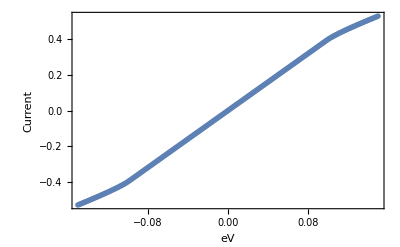

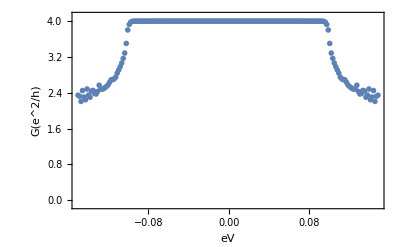

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Two site Floquet

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
t=1.0; (*Lattice constant*)
B=1.7; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0000001; (*Imaginary off-set*)
Ln=0;
it=1000;

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];
Id8=IdentityMatrix[8];

eVmin=-0.02; (*Minimal bias value*)
eVmax=0.02; (*Maximal bias value*)
NeV=201; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,μ_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω-μ],T],FermiFunction[Re[ω-μ],T],1-FermiFunction[Re[-ω-μ],T],1-FermiFunction[Re[-ω-μ],T]}];
```

```mathematica
ΣInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	V10.gL.V01
	];	
	
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];	

gInfLesser[ω_, μ_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, μ, T].(gr - ga)
];	

ΣInfLess[ω_, μ_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{gless = gInfLesser[ω, μ, T, HS, V01, V10, η, it, HN, Ln]},
  V10.gless.V01
];
		
zeros = ConstantArray[0, {4, 4}];	
ΣEmbedL[Σ_]:= ArrayFlatten[{{Σ, zeros}, {zeros, zeros}}];	
ΣEmbedR[Σ_]:= ArrayFlatten[{{zeros, zeros}, {zeros, Σ}}];

nBand=0;
nb=2nBand+1;
μ=0.0;
ΣLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInf[ε + 0(n - 1 - nBand) eV, HN, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInf[ε + 0(n - 1 - nBand) eV, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

ΣLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInfLess[ε + 0(n - 1 - nBand) eV, eV, T, HN, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInfLess[ε + 0(n - 1 - nBand) eV, 0, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInf[ε + 0(n - 1 - nBand) eV, HN, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInf[ε + 0(n - 1 - nBand) 0, HS, V10, V01, η, it,HN,Ln]],{n, nb}]]; 

gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInfLesser[ε + 0(n - 1 - nBand) eV, eV, T, HN, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInfLesser[ε + 0(n - 1 - nBand) eV, 0, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]];
```

```mathematica
H0=ArrayFlatten[{{HN, ConstantArray[0, Dimensions[HS]]},
                  {ConstantArray[0, Dimensions[HN]], HN}}];	
VP=ArrayFlatten[{{ConstantArray[0, Dimensions[HS]], ConstantArray[0, Dimensions[HS]]},
                  {V01, ConstantArray[0, Dimensions[HS]]}}];        
VM=ConjugateTranspose[VP];   

HF[eV_] := ArrayFlatten@Table[
    Which[
      n == m, H0 - (n - 1 - nBand) eV Id8,     (* diagonal block with −n ω0 shift *)
      n == m + 1, VP,                        (* coupling to lower sideband *)
      n == m - 1, VM,                         (* coupling to upper sideband *)
      True, ConstantArray[0, {8, 8}]
    ],
    {n, nb}, {m, nb}
  ];      
  
τ4 = DiagonalMatrix[{1, 1, -1, -1}];
zeros4 = ConstantArray[0, {4, 4}];
τ8 = ArrayFlatten[{{τ4, zeros4}, {zeros4, τ4}}];

(* Floquet lift: repeat across sidebands *)
τFloq = KroneckerProduct[IdentityMatrix[2 nBand + 1], τ8];
```

```mathematica
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,eV_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[ω-eV],T]}];
U=DiagonalMatrix[{1,1,-1,-1,1,1,-1,-1}];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<=0), ωmin=eV-8 T; ωmax=-eV+8 T
];

ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	(*ω=I η;*)
	gLesserL=gLesserLFloq[ω, eV];
	gLesserR=gLesserRFloq[ω, eV];
	
	ΣL=ΣLFloq[ω, eV];
	ΣR=ΣRFloq[ω, eV];
	
	ΣLesserL=ΣLesserLFloq[ω, eV];
	ΣLesserR=ΣLesserRFloq[ω, eV];
	
	G=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR];
	
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];
	

	(*gLesserL=-F[ω,eV,T].(gLLr-gLLa);
	gLesserR=-F[ω,0,T].(gRRr-gRRa);
	
	ΣLesserL=V10.gLesserL.V01;
	ΣLa=V10.gLLa.V01;
	ΣLesserR=V01.gLesserR.V10;
	
	G=Inverse[ω Id-HL-V10.gLLr.V01-V01.gRRr.V10];
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];*)

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣL).U]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)
	,{EnergyIt,1,Nω}];

	(*,{EnergyIt,1,Nω}];*)

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,1,NeV}];
(*,{eVIter,1,NeV}];*)
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.995291+25660. ⅈ,-1.30453-25800.9 ⅈ,-0.0767818-25800.9 ⅈ,0.0000527978-25660. ⅈ},«2»,{0.0000527979-25660. ⅈ,-0.076888+«18» ⅈ,-«19»+«1»,0.995185+25660. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

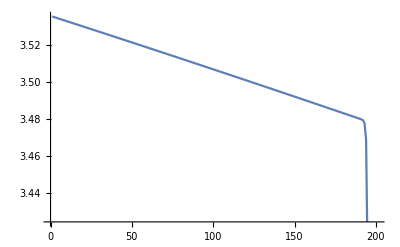

```mathematica
ListLinePlot[Current]
```

```mathematica
ΣR//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00477333-25660. ⅈ | -0.395403+25800.9 ⅈ | -0.0231539+25800.9 ⅈ | 0.0000109809+25660. ⅈ
0 | 0 | 0 | 0 | -0.395403+25800.9 ⅈ | -0.0910827-25942.6 ⅈ | -0.0000112837-25942.6 ⅈ | -0.0231761-25800.9 ⅈ
0 | 0 | 0 | 0 | -0.023154+25800.9 ⅈ | -0.0000111692-25942.6 ⅈ | 0.0910603-25942.6 ⅈ | -0.395425-25800.9 ⅈ
0 | 0 | 0 | 0 | 0.0000110844+25660. ⅈ | -0.0231762-25800.9 ⅈ | -0.395425-25800.9 ⅈ | 0.00475126-25660. ⅈ)

```mathematica
Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.910384+0.444317 ⅈ,-1.30438-0.468638 ⅈ,0.+0. ⅈ,«3»,0.+0. ⅈ,0.+0. ⅈ},«6»,{«1»}} may contain significant numerical errors.

{{-0.0498124-0.489964 ⅈ,-0.396974+0.467624 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.396974+0.467624 ⅈ,-0.0425716-0.446304 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.0425716-0.446304 ⅈ,-0.396974-0.467624 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.396974-0.467624 ⅈ,0.0498124-0.489964 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0434294-25085.6 ⅈ,-0.396188+25512.1 ⅈ,0.00774107-25512.1 ⅈ,0.0000107673-25085.6 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.396188+25512.1 ⅈ,-0.0505761-25945.9 ⅈ,-0.0000111163+25945.9 ⅈ,0.00771918+25512.1 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.00774105-25512.1 ⅈ,-0.0000111206+25945.9 ⅈ,0.0505983-25945.9 ⅈ,-0.396166-25512.1 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0000107751-25085.6 ⅈ,0.00771916+25512.1 ⅈ,-0.396166-25512.1 ⅈ,0.043451-25085.6 ⅈ}}

```mathematica
G//MatrixForm
```

(-0.0498124-0.489964 ⅈ | -0.396974+0.467624 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-0.396974+0.467624 ⅈ | -0.0425716-0.446304 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.0425716-0.446304 ⅈ | -0.396974-0.467624 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.396974-0.467624 ⅈ | 0.0498124-0.489964 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0434294-25085.6 ⅈ | -0.396188+25512.1 ⅈ | 0.00774107-25512.1 ⅈ | 0.0000107673-25085.6 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.396188+25512.1 ⅈ | -0.0505761-25945.9 ⅈ | -0.0000111163+25945.9 ⅈ | 0.00771918+25512.1 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.00774105-25512.1 ⅈ | -0.0000111206+25945.9 ⅈ | 0.0505983-25945.9 ⅈ | -0.396166-25512.1 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.0000107751-25085.6 ⅈ | 0.00771916+25512.1 ⅈ | -0.396166-25512.1 ⅈ | 0.043451-25085.6 ⅈ)

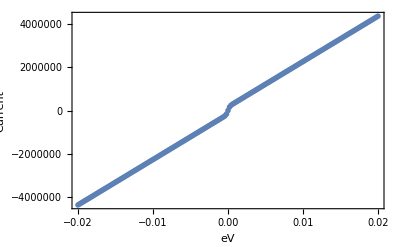

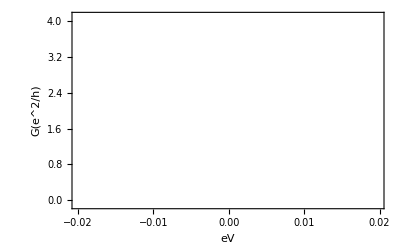

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# One site Floquet

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.0; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0000001; (*Imaginary off-set*)
Ln=0;
it=1000;

nBand=15;
nb=2nBand+1;

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];

eVmin=0.0; (*Minimal bias value*)
eVmax=0.3; (*Maximal bias value*)
NeV=101; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
```

```mathematica
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,eV_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω-eV],T],FermiFunction[Re[ω-eV],T],1-FermiFunction[Re[-ω-eV],T],1-FermiFunction[Re[-ω-eV],T]}];
U=DiagonalMatrix[{1,1,-1,-1}];
UFloq=KroneckerProduct[IdentityMatrix[nb],U];
```

```mathematica
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];
	
ΣInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	V10.gL.V01
	];		
	
gInfLesser[ω_, μ_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, μ, T].(gr - ga)
];

ΣInfLess[ω_, μ_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{gless = gInfLesser[ω, μ, T, HS, V01, V10, η, it, HN, Ln]},
  V10.gless.V01
];

ΣInfa[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{g = gInf[ω,HS,V01,V10,η,it,HN,Ln]},
  V10.ConjugateTranspose[g].V01
];			

ΣLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣInf[ε + (n - 1 - nBand) eV, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
ΣRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣInf[ε + (n - 1 - nBand) eV, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

ΣaFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣInfa[ε + (n - 1 - nBand) eV, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
		
gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε + (n - 1 - nBand) eV, 0, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInf[ε + (n - 1 - nBand) eV, 0, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε + (n - 1 - nBand) eV, 0, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[gInfLesser[ε + (n - 1 - nBand) eV, 0, T, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 

ΣLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣInfLess[ε + (n - 1 - nBand) eV, 0, T, HS, V01, V10, η, it, HN, Ln],{n, nb}]]; 
ΣLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣInfLess[ε + (n - 1 - nBand) eV, 0, T, HS, V10, V01, η, it, HN, Ln],{n, nb}]]; 
					
HF[eV_] := ArrayFlatten@Table[
    Which[
      n == m, HS - (n - 1 - nBand) eV Id,     (* diagonal block with −n ω0 shift *)
      n == m + 1, V01,                        (* coupling to lower sideband *)
      n == m - 1, V10,                         (* coupling to upper sideband *)
      True, ConstantArray[0, {4, 4}]
    ],
    {n, nb}, {m, nb}
  ];
```

```mathematica
τ=1.0;
Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

(*Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];*)

ωmin=0.0;
ωmax=eV;
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	gLesserL=gLesserLFloq[ω, eV];
	gLesserR=gLesserRFloq[ω, eV];
	
	ΣL=ΣLFloq[ω, eV];
	ΣR=ΣRFloq[ω, eV];
	
	ΣLesserL=ΣLesserLFloq[ω, eV];
	ΣLesserR=ΣLesserRFloq[ω, eV];
	
	ΣLa=ΣaFloq[ω,eV];
	
	G=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR];
	
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).UFloq]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)

	,{EnergyIt,1,Nω}];

CurrentList[[eVIter,2]]=Total[Current] Abs[ωsteps];

,{eVIter,NeV,NeV}];
```

```mathematica
CurrentList[[-1]]
```

{0.3,-0.000937026}

```mathematica
CurrentList[[-1]]
```

{0.3,-0.000936538}

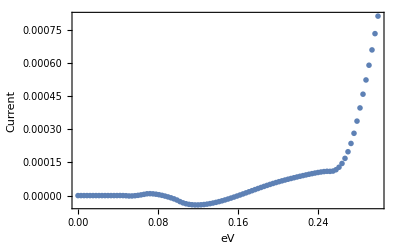

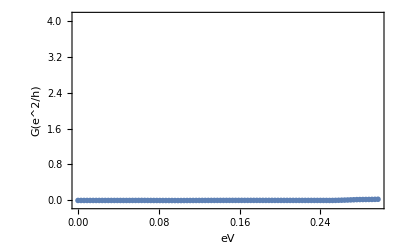

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Two site Floquet

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
Ithis=0.0;
lastI=Pi;
tol = 1.*10^-7;
Nn=35;

eVmin=0.0; (*Minimal bias value*)
eVmax=0.3; (*Maximal bias value*)
NeV=101; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
Nω=201; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

Do[
If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

lastI = 0;
converged = False;

Do[

t=1.0; (*Lattice constant*)
B=0.0; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
η=0.0001; (*Imaginary off-set*)
Ln=0;
it=1000;

nBand=nIter;
nb=2nBand+1;

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];
Id8=IdentityMatrix[8];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],1-FermiFunction[Re[-ω],T],1-FermiFunction[Re[-ω],T]}];
U=DiagonalMatrix[{1,1,-1,-1,1,1,-1,-1}];
UFloq=KroneckerProduct[IdentityMatrix[nb],U];
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];
	
ΣInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	V10.gL.V01
	];		
	
gInfLesser[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, T].(gr - ga)
];

ΣInfLess[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{gless = gInfLesser[ω, T, HS, V01, V10, η, it, HN, Ln]},
  V10.gless.V01
];

ΣInfa[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{g = gInf[ω,HS,V01,V10,η,it,HN,Ln]},
  V10.ConjugateTranspose[g].V01
];			

zeros = ConstantArray[0, {4, 4}];	
ΣEmbedL[Σ_]:= ArrayFlatten[{{Σ, zeros}, {zeros, zeros}}];	
ΣEmbedR[Σ_]:= ArrayFlatten[{{zeros, zeros}, {zeros, Σ}}];

ΣLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInf[ε + (n - 1 - nBand)2 eV, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInf[ε + (n - 1 - nBand)2 eV, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

ΣaFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInfa[ε + (n - 1 - nBand)2 eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 	
	
gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInf[ε + (n - 1 - nBand)2 eV, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInf[ε + (n - 1 - nBand)2 eV, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInfLesser[ε + (n - 1 - nBand)2 eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInfLesser[ε + (n - 1 - nBand)2 eV, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

ΣLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInfLess[ε + (n - 1 - nBand)2 eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInfLess[ε + (n - 1 - nBand)2 eV, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

zeros = ConstantArray[0, {4, 4}];

H0 = ArrayFlatten[{
  {HN, zeros},
  {zeros, HS}
}];					
															
VP = ArrayFlatten[{
  {zeros, V10},
  {zeros, zeros}
}];

VM = ArrayFlatten[{
  {zeros, zeros},
  {V01,  zeros}
}];
    
HF[eV_] := ArrayFlatten@Table[
    Which[
      n == m, H0 - (n - 1 - nBand)2 eV Id8,     (* diagonal block with −n ω0 shift *)
      n == m + 1, VM,                        (* coupling to lower sideband *)
      n == m - 1, VP,                         (* coupling to upper sideband *)
      True, ConstantArray[0, {8, 8}]
    ],
    {n, nb}, {m, nb}
  ];        			
τ=1.0;

(*Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];*)

ωmin=0.0;
ωmax=2 eV;
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	gLesserL=gLesserLFloq[ω, eV];
	gLesserR=gLesserRFloq[ω, eV];
	
	ΣL=ΣLFloq[ω, eV];
	ΣR=ΣRFloq[ω, eV];
	
	ΣLesserL=ΣLesserLFloq[ω, eV];
	ΣLesserR=ΣLesserRFloq[ω, eV];
	
	ΣLa=ConjugateTranspose[ΣL];
	
	G=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR];
	
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).UFloq]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)

	,{EnergyIt,1,Nω}];
	(*CurrentList[[eVIter, 2]] =Total[Current]*Abs[ωsteps];*)
	Ithis=Total[Current]*Abs[ωsteps];
	If[nBand>4 && Abs[Ithis - lastI] < tol,
        CurrentList[[eVIter, 2]] = Ithis;
        converged = True;
        Break[];
      ];
   lastI=Ithis;  
,{nIter,1,Nn}]
,{eVIter,1,NeV}];
```

10

20

30

40

50

60

70

80

90

100

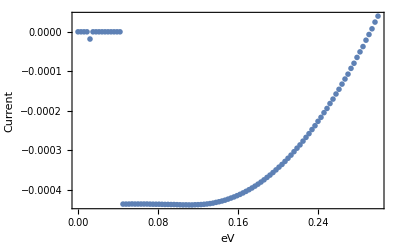

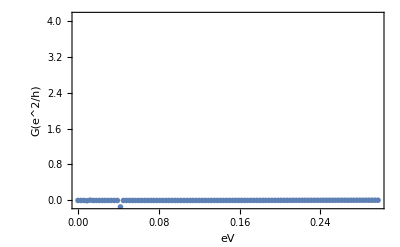

```mathematica
(* Set the default color to MATLAB's default color *)
SetOptions[ListPlot, PlotStyle -> ColorData[97]];

(* Plot 1: current vs bias *)
ListPlot[Table[{CurrentList[[i, 1]], CurrentList[[i, 2]]}, {i, 1, NeV}], 
  Frame -> True, 
  FrameLabel -> {"eV", "Current"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> All (* Adjust plot range *)
]

(* Plot 2: conductance vs bias *)
Conductance = Differences[CurrentList[[1 ;; All, 2]]]/Differences[CurrentList[[1 ;; All, 1]]];
ListPlot[Table[{CurrentList[[i, 1]], Conductance[[i]]}, {i, 1, NeV - 1}], 
  Frame -> True, 
  FrameLabel -> {"eV", "G(e^2/h)"},
  PlotStyle -> PointSize[0.01], (* Adjust point size *)
  PlotRange -> {All,{-0.1,4.1}} (* Adjust plot range *)
]

(* Reset the default color *)
SetOptions[ListPlot, PlotStyle -> Automatic];
```

# Two site Floquet Check

```mathematica
Clear["Global`*"]
```

```mathematica
(* fallback for older Mathematica versions *)
BlockDiagonalMatrix[mats_List] := 
  ArrayFlatten[
    Table[
      If[i == j, mats[[i]], 
        ConstantArray[0, Dimensions[mats[[1]]]]
      ],
      {i, Length[mats]}, {j, Length[mats]}
    ]
  ];
```

```mathematica
LaunchKernels[];
SetSharedVariable[CurrentList];

Ithis=0.0;
lastI=Pi;
δ=0.00000001;
tol = 1.*10^-3;
Nn=50;

eVmin=0.0; (*Minimal bias value*)
eVmax=0.3; (*Maximal bias value*)
NeV=101; (*Number of steps in the bias loop*)
stepseV=(eVmax-eVmin)/(NeV-1);

Nmin=34;
Nmax=6;
stepsN=(Nmax-Nmin)/(NeV-1);

Current=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];
Nω=401; (*Number of steps in the energy loop*)
Current=Table[0,{i,1,Nω}];
CurrentList=Table[{(i-1)stepseV+eVmin,0},{i,1,NeV}];

Monitor[
ParallelDo[

If[IntegerQ[eVIter/10],Print[eVIter]];
eV=(eVIter-1)stepseV+eVmin; (*Applied bias*)

lastI = 0;
last = 0;
converged = False;

Do[

t=1.0; (*Lattice constant*)
B=1.7; (*Magnetic field in x-direction 1.7*)
α=0.05; (*Spin-orbit coupling 0.05*)
Δ=0.1; (*Superconducting pairing*)
μL=1.0; (*Chemical potential of the left lead*)
μR=1.0; (*Chemical potential of the right lead*)
T=0.0001; (*Temperature*)
Tn=0.05;
η=0.0001; (*Imaginary off-set*)
Ln=0;
it=1000;

nBand=nIter;
nb=2nBand+1;

HS={{2t-μR,B,Δ,0},{B,2t-μR,0,Δ},{Δ,0,-(2t-μR),B},{0,Δ,B,-(2t-μR)}};
HN={{2t-μL,B,0,0},{B,2t-μL,0,0},{0,0,-(2t-μL),B},{0,0,B,-(2t-μL)}};
V01={{-t,α t,0,0},{-α t,-t,0,0},{0,0,t,-α t},{0,0,α t,t}};
V10=ConjugateTranspose[V01];
V01r=Tn*{{-t,α t},{-α t,-t}};

ΣLRr=V01;
ΣRLr=V10;
ΣLRa=ConjugateTranspose[ΣRLr];
ΣRLa=ConjugateTranspose[ΣLRr];

Id=IdentityMatrix[4];
Id8=IdentityMatrix[8];

(*Fermi functions*)
FermiFunction[x_,y_]:=If[y==0,Which[x<0,1,x==0,1/2,x>0,0],If[x/y>20,0.0,If[x/y<-20, 1,Quiet[ 1/(Exp[x/y]+1)]]]];
F[ω_,T_]:=DiagonalMatrix[{FermiFunction[Re[ω],T],FermiFunction[Re[ω],T],1-FermiFunction[Re[-ω],T],1-FermiFunction[Re[-ω],T]}];
U=DiagonalMatrix[{1,1,-1,-1,1,1,-1,-1}];
UFloq=KroneckerProduct[IdentityMatrix[nb],U];
gInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	gL
	];
	
ΣInf[ω_,HS_,V01_,V10_,η_,it_,HN_,Ln_]:=Module[{g,gL,ϵ,ϵS,α,β,Id},
	Id=IdentityMatrix[Length[HS]];
	(*Semiinfinite superconductor*)
	g=Inverse[ω Id-HS]; ϵ=HS;ϵS=HS;α=V10;β=V01;
	Do[ϵS=ϵS+α.g.β;ϵ=ϵ+α.g.β+β.g.α;α=α.g.α;β=β.g.β;g=Inverse[ω Id-ϵ];
		If[Max[Abs[α]]<10^-15,Break[];],{i,1,it}];
	gL=Inverse[ω Id-ϵS];
	(*Finite normal part*)
	Do[gL=Inverse[ω Id-HN-V10.gL.V01],{i,1,Ln}];
	V10.gL.V01
	];		
	
gInfLesser[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[
  {gr = gInf[ω,HS,V01,V10,η,it,HN,Ln], ga},
  ga = ConjugateTranspose[gr];
  - F[ω, T].(gr - ga)
];

ΣInfLess[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{gless = gInfLesser[ω, T, HS, V01, V10, η, it, HN, Ln]},
  V10.gless.V01
];

ΣInfa[ω_, T_, HS_, V01_, V10_, η_, it_, HN_, Ln_] := Module[{g = gInf[ω,HS,V01,V10,η,it,HN,Ln]},
  V10.ConjugateTranspose[g].V01
];			

zeros = ConstantArray[0, {4, 4}];	
ΣEmbedL[Σ_]:= ArrayFlatten[{{Σ, zeros}, {zeros, zeros}}];	
ΣEmbedR[Σ_]:= ArrayFlatten[{{zeros, zeros}, {zeros, Σ}}];

ΣLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInf[ε + (n - 1 - nBand) eV, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInf[ε + (n - 1 - nBand) eV, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

ΣaFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInfa[ε + (n - 1 - nBand) eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 	
	
gLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInf[ε + (n - 1 - nBand) eV, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInf[ε + (n - 1 - nBand) eV, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

gLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[gInfLesser[ε + (n - 1 - nBand) eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
gLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[gInfLesser[ε + (n - 1 - nBand) eV, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

ΣLesserLFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedL[ΣInfLess[ε + (n - 1 - nBand) eV, T, HS, V01, V10, η, it, HN, Ln]],{n, nb}]]; 
ΣLesserRFloq[ε_, eV_] := BlockDiagonalMatrix[Table[ΣEmbedR[ΣInfLess[ε + (n - 1 - nBand) eV, T, HS, V10, V01, η, it, HN, Ln]],{n, nb}]]; 

zeros = ConstantArray[0, {4, 4}];

H0 = ArrayFlatten[{
  {HS, zeros},
  {zeros, HS}
}];					
															
Z[v_]:=ConstantArray[0,Dimensions[v]];
HSplus1[v0_]:=ArrayFlatten[{{Z[v0],Z[v0],Z[v0],Z[v0]},{Z[v0],Z[v0],Z[v0],-Transpose[v0]},{v0,Z[v0],Z[v0],Z[v0]},{Z[v0],Z[v0],Z[v0],Z[v0]}}];		
HSminus1[v0_]:=ArrayFlatten[{{Z[v0],Z[v0],ConjugateTranspose[v0],Z[v0]},{Z[v0],Z[v0],Z[v0],Z[v0]},{Z[v0],Z[v0],Z[v0],Z[v0]},{Z[v0],-Conjugate[v0],Z[v0],Z[v0]}}];
VM=HSminus1[V01r];
VP=HSplus1[V01r];												
    
HF[eV_] := ArrayFlatten@Table[
    Which[
      n == m, H0 - (n - 1 - nBand) eV Id8,     (* diagonal block with −n ω0 shift *)
      n == m + 1, VM,                        (* coupling to lower sideband *)
      n == m - 1, VP,                         (* coupling to upper sideband *)
      True, ConstantArray[0, {8, 8}]
    ],
    {n, nb}, {m, nb}
  ];        			
τ=1.0;

(*Which[  (eV>0), ωmin=-eV-8 T; ωmax=eV+8 T,
		(eV<0), ωmin=eV-8 T; ωmax=-eV+8 T
];*)

ωmin=0.0;
ωmax=eV;
ωsteps=(ωmax-ωmin)/(Nω-1); (*Energy*)
Do[
	ω=(EnergyIt-1)ωsteps+ωmin+I η;
	
	gLesserL=gLesserLFloq[ω, eV];
	gLesserR=gLesserRFloq[ω, eV];
	
	ΣL=ΣLFloq[ω, eV];
	ΣR=ΣRFloq[ω, eV];
	
	ΣLesserL=ΣLesserLFloq[ω, eV];
	ΣLesserR=ΣLesserRFloq[ω, eV];
	
	ΣLa=ConjugateTranspose[ΣL];
	
	G=Inverse[ω IdentityMatrix[Length[HF[eV]]]-HF[eV]-ΣL-ΣR];
	
	GLesser=G.(ΣLesserL+ΣLesserR).ConjugateTranspose[G];

	Current[[EnergyIt]]=Re[Tr[(G.ΣLesserL+GLesser.ΣLa).UFloq]]	
	(* Setting up the non-equilibrium Green's functions for the metal and the superconductor *)
	(*gLLPM=(gLLa-gLLr).F[ω,eV,T];
	gRRPM=(gRRa-gRRr).F[ω,0,T];
	GRRa=Inverse[Id-gRRa.ΣRLa.gLLa.ΣLRa].gRRa;
	GRRr=ConjugateTranspose[GRRa];
	GRLr=Inverse[Id-gRRr.ΣRLr.gLLr.ΣLRr].gRRr.ΣRLr.gLLr;
	GLRa=ConjugateTranspose[GRLr];
	GRRPM=(Id+GRLr.ΣLRr).gRRPM.(Id+ΣRLa.GLRa)+GRRr.ΣRLr.gLLPM.ΣLRa.GRRa;
	GLRPM=gLLPM.ΣLRa.GRRa+gLLr.ΣLRr.GRRPM;
	GRLPM=GRRPM.ΣRLa.gLLa+GRRr.ΣRLr.gLLPM;
	Current[[EnergyIt]]=Total[Diagonal[(ΣLRr.GRLPM-ΣRLa.GLRPM).U]];*)

	,{EnergyIt,1,Nω}];
	(*CurrentList[[eVIter, 2]] =Total[Current]*Abs[ωsteps];*)
	Ithis=-Total[Current]*Abs[ωsteps];
	CurrentList[[eVIter, 2]] = Ithis;
	If[Abs[Ithis - lastI]/(Ithis + lastI+δ) < tol,
        CurrentList[[eVIter, 2]] = Ithis;
        converged = True;
        Break[];
      ];
   last=lastI; 
   lastI=Ithis;
,{nIter,Ceiling[(eVIter-1)stepsN+Nmin],Nn}]
,{eVIter,1,20}],
eVIter
];

SetDirectory[NotebookDirectory[]];
Export["Floquet_18.11.2025_B="<>ToString[B]<>"_T="<>ToString[Tn]<>".mx",CurrentList];
Export["Floquet_18.11.2025_B="<>ToString[B]<>"_T="<>ToString[Tn]<>".png",ListLinePlot[CurrentList]];
```

```mathematica
Ithis
```

0.0000571065

```mathematica
lastI
```

0.0000571309

```mathematica
Ithis
```

0.0000558331

```mathematica
lastI
```

0.0000558574

```mathematica
Ithis
```

0.0000554086

```mathematica
lastI
```

0.000055433

```mathematica
Ithis
```

0.0000552771

```mathematica
lastI
```

0.0000553047

```mathematica
Ithis-lastI
```

-2.76126×10^-8

```mathematica
Ithis
```

0.0000552771

```mathematica
lastI
```

0.0000553047

```mathematica
Abs[Ithis - lastI]/(Ithis + lastI+δ)<10^(-3)
```

True

```mathematica
Abs[Ithis - lastI]/(Ithis + lastI+δ)<tol
```

True

```mathematica
Ithis
```

0.000424511

```mathematica
lastI
```

0.00042442

```mathematica
Ithis
```

0.00297956

```mathematica
lastI
```

0.00297966

```mathematica
nBand
```

35

```mathematica
last
```

0

```mathematica
lastI
```

0.0410265

```mathematica
Ithis
```

0.0410265

```mathematica
nBand
```

7

```mathematica
N[10^(-3)]
```

0.001

```mathematica
nBand
```

119

```mathematica
Ithis
```

0.000658283

```mathematica
last
```

0.000652317

```mathematica
Ithis
```

0.000790552

```mathematica
lastI
```

0.000790552

```mathematica
Abs[Ithis - lastI]/(Ithis + lastI+δ)
```

1.02129×10^-9

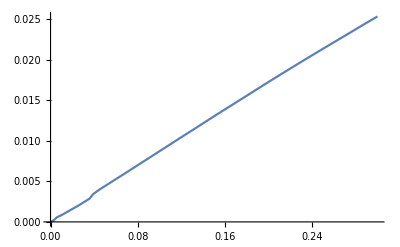

```mathematica
ListLinePlot[CurrentList]
```

```mathematica
Abs[Ithis - last]/(Ithis + last+δ)
```

0.0113445

```mathematica
Ithis
```

0.0000242482

```mathematica
Ithis
```

0.0000242482

```mathematica
lastI
```

0.0000242482

```mathematica
last
```

0.0000185594